```mathematica
$Assumptions={e>0&&e<1&&aa>0&&nn>0&&m>0&&y>0&&ν>0&&θ1>0&&θ1<Pi&&ψ1>-Pi&&ψ1<Pi&&u>-Pi&&u<Pi&&χ>-1&&χ<1};
```

## Compute Leading Order Tidal Heating and Torquing for arbitrary orbits

```mathematica
<<xAct`xTensor`
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2026, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
(*Define 3-dimensional manifold to perform our computations*)
DefManifold[M3,3,{a,b,c,d,f,g,h,i,j}]
(*Define the tensors we need*)
DefMetric[1,metric[-a,-b],cd,{"|","D"},PrintAs->"g",FlatMetric->True]
DefTensor[s1[a],M3]
DefTensor[S1hat[a,b],M3]
DefTensor[x[a],M3]
DefTensor[xdot[a],M3]
DefTensor[l[a],M3]
DefTensor[EE[a,b],M3]
DefTensor[QE[a,b],M3]
DefTensor[EEdot[a,b],M3]
DefTensor[dJ1dt[a],M3]
(*Constants that will be used*)
DefConstantSymbol/@{m1,m2,χ1,s1n,s1l,r,f01,f10,f30,v,vn};
```

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

** DefTensor: Defining symmetric metric tensor metric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetric[-a,-b,-c].

** DefCovD: Defining covariant derivative cd[-a].

** DefTensor: Defining vanishing torsion tensor Torsioncd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor Christoffelcd[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor Riemanncd[-a,-b,-c,-d].

** DefTensor: Defining vanishing Ricci tensor Riccicd[-a,-b].

** DefTensor: Defining vanishing Ricci scalar RicciScalarcd[].

** DefTensor: Defining vanishing Einstein tensor Einsteincd[-a,-b].

** DefTensor: Defining vanishing Weyl tensor Weylcd[-a,-b,-c,-d].

** DefTensor: Defining vanishing TFRicci tensor TFRiccicd[-a,-b].

** DefTensor: Defining vanishing Kretschmann scalar Kretschmanncd[].

** DefTensor: Defining weight +2 density Detmetric[].      Determinant.

** DefTensor: Defining tensor s1[a].

** DefTensor: Defining tensor S1hat[a,b].

** DefTensor: Defining tensor x[a].

** DefTensor: Defining tensor xdot[a].

** DefTensor: Defining tensor l[a].

** DefTensor: Defining tensor EE[a,b].

** DefTensor: Defining tensor QE[a,b].

** DefTensor: Defining tensor EEdot[a,b].

** DefTensor: Defining tensor dJ1dt[a].

** DefConstantSymbol: Defining constant symbol m1.

** DefConstantSymbol: Defining constant symbol m2.

** DefConstantSymbol: Defining constant symbol χ1.

** DefConstantSymbol: Defining constant symbol s1n.

** DefConstantSymbol: Defining constant symbol s1l.

** DefConstantSymbol: Defining constant symbol r.

** DefConstantSymbol: Defining constant symbol f01.

** DefConstantSymbol: Defining constant symbol f10.

** DefConstantSymbol: Defining constant symbol f30.

** DefConstantSymbol: Defining constant symbol v.

** DefConstantSymbol: Defining constant symbol vn.

```mathematica
(*Define simplifications*)
s1/:s1[a_]s1[-a_]:=1
s1/:s1[a_]x[-a_]:=r s1n
s1/:epsilonmetric[-a_,-b_,-c_] s1[a_] x[b_] xdot[c_]:=s1l
x/:x[a_]x[-a_]:=r^2
x/:x[a_]xdot[-a_]:=r vn
x/:epsilonmetric[  a_,-b_,-c_]  x[b_] xdot[c_]:=l[a]
l/:s1[-a_]l[a_]:=s1l
xdot/:xdot[a_]xdot[-a_]:=v^2
```

```mathematica
(*Compute leading order tidal field, in agreement with Eq.(10) of 2408.15322*)
IndexSet[EE[a_,b_],-m2/r^3(3 1/r^2 x[a]x[b]-delta[a,b])];
(*Compute time derivative of leading order tidal field*)
IndexSet[EEdot[a_,b_],-3 m2/r^5(xdot[a]x[b]+x[a]xdot[b]-xdot[c]x[-c](5 1/r^2 x[a]x[b]-delta[a,b]))];
(*Spin tensor*)
IndexSet[S1hat[a_,b_],epsilonmetric[a,b,-c]s1[c]];
(*Compute the mass quadrupole moment of a generic object, following the notation of 2212.13095*)
IndexSet[QE[a_,b_],m1^5(f10(1/2(EE[a,c] epsilonmetric[b,-c,-d]+EE[b,c] epsilonmetric[a,-c,-d]))s1[d]+f30 (1/2(s1[a]epsilonmetric[b,-c,-d]+s1[b]epsilonmetric[a,-c,-d]))EE[c,-j]s1[d]s1[j] + m1 f01 EEdot[a,b])];
```

```mathematica
(*Compute Leading Order dm/dt*)
dm1$dt=Simplification[ToCanonical[ContractMetric[1/2 QE[a,b]EEdot[-a,-b]]]];
Simplify[-9/2 (m1^5 m2^2)/r^8 (( f10+f30 s1n^2)s1l-2 m1 f01 (v^2+2 vn^2))-dm1$dt]
(*Compare with Leading Order dm/dt from Eq.(14a) of 2408.15322*)
dm1$dt240815322=Simplification[ToCanonical[ContractMetric[m1^5/2(f10 (EEdot[a,b]EE[-a,c]S1hat[-b,-c])+f30(EEdot[-a,c]EE[-b,d]s1[a]s1[b]S1hat[-c,-d])+ m1 f01 EEdot[a,b] EEdot[-a,-b])]]];
Simplify[dm1$dt240815322-dm1$dt]
```

0

0

```mathematica
(*Compute Leading Order dJ^a/dt*)
dJ1dt[a_]:=Simplification[ToCanonical[ContractMetric[-epsilonmetric[a,-b,-c]QE[b,-d]EE[d,c]]]];
Simplify[-(9 m1^5 m2^2)/(2 r^6)((f10+f30 s1n^2) ({{s1, {{a}, {}}}}-s1n/r {{x, {{a}, {}}}})-(2 f01 m1 {{l, {{a}, {}}}})/r^2)-dJ1dt[a]]
(*Compare with leading dS1/dt from Eq.(14b) of 2408.15322*)
EEss=Simplification[ToCanonical[ContractMetric[EE[-a,-b]s1[a]s1[b]]]];
dS1$dt240815322=Simplification[ToCanonical[ContractMetric[m1^5/2(-2f10(EE[-a,-b]EE[a,b])+(3f10-f30)(EE[-a,-c]EE[-b,c]s1[a]s1[b])+f30 EEss^2-m1(2 f01 EEdot[a,b]EE[-a,c]S1hat[-b,-c]))]]];
Simplify[dS1$dt240815322-Simplification[ToCanonical[ContractMetric[dJ1dt[-a]s1[a]]]]]
```

0

0

```mathematica
(*Separate terms proportional to s1[a], x[a] and l[a]*)
dS1$dts=SeriesCoefficient[dJ1dt[a],{s1[a],0,1}];
dS1$dtx=SeriesCoefficient[dJ1dt[a],{x[a],0,1}];
dS1$dtl=SeriesCoefficient[dJ1dt[a],{l[a],0,1}];
Simplify[-(9 m1^5 m2^2)/(2 r^6)(f10+f30 s1n^2)-dS1$dts]
Simplify[(9 m1^5 m2^2)/(2 r^6)(f10+f30 s1n^2)s1n/r-dS1$dtx]
Simplify[(9 f01 m1^6 m2^2)/r^8-dS1$dtl]
Simplify[dS1$dts s1[a] + dS1$dtx x[a] + dS1$dtl l[a]-dJ1dt[a]]
```

0

0

0

«1 more identical outputs»

## Orbit averaged tidal heating and torquing effects for Keplerian orbits

```mathematica
(*Kepler orbit in Cartesian coordinates*)
keprules={xx->aa(Cos[u]-e), yy->aa √(1-e^2)Sin[u],xxdot->nn aa(-Sin[u])/(1-e Cos[u]),yydot->nn aa(√(1-e^2) Cos[u])/(1-e Cos[u]),r->aa (1-e Cos[u]),v->nn aa √((1+e Cos[u])/(1-e Cos[u])),vn->nn aa(e Sin[u])/(1-e Cos[u]),s1l->aa^2 √(1-e^2) nn s1z,s1n->(s1x (Cos[u]-e)+s1y √(1-e^2)Sin[u])/(1-e Cos[u])};
(*Simplification rules*)
simpspins={s1x->Sin[θ1]Cos[ψ1],s1y->Sin[θ1]Sin[ψ1],s1z->Cos[θ1]};
simpEFPE={aa->m/((1-e^2)y^2),nn->((1-e^2)^(3/2)y^3)/m,m1->μ1 m, m2->μ2 m};
(*Check different parts of our kepler rules*)
Simplify[nn D[xx/.keprules,u]/(1-e Cos[u])-xxdot/.keprules ]
Simplify[nn D[yy/.keprules,u]/(1-e Cos[u])-yydot/.keprules ]
Simplify[(√(xx^2+yy^2) -r)/.keprules]
Simplify[(√(xxdot^2+yydot^2) -v)/.keprules]
Simplify[(({xx,yy,0}.{xxdot,yydot,0})/r-vn)/.keprules]
(*Check the value of angular momentum vector l[a]=epsilonmetric[a,-b,-c] x[b] xdot[c]*)
lKepNorm=m/y;
lKep = {0,0,lKepNorm};
Simplify[(((({xx,yy,0}×{xxdot,yydot,0}))/.keprules)-lKep)/.simpEFPE]
(*Check the value of s1.l=epsilonmetric[-a,-b,-c] s1[a] x[b] xdot[c]*)
Simplify[(({s1x,s1y,s1z}.lKep)-s1l)/.keprules/.simpEFPE]
(*Check the value of s1.n=s1[a] x[-a]*)
Simplify[(({s1x,s1y,s1z}.{xx,yy,0})/(√(xx^2+yy^2))-s1n)/.keprules]
```

0

0

0

«2 more identical outputs»

{0,0,0}

0

0

```mathematica
(*Compute instantaneous expressions for tidal heating and torquing, using D=m/((1-e^2)^(3/2))d/dt from Eq.(4) of 2106.10291*)
Dm1Kep=Simplify[(m/((1-e^2)^(3/2)) dm1$dt)/.keprules/.simpspins/.simpEFPE];
DS1sKep=Simplify[(m/((1-e^2)^(3/2)) dS1$dts)/.keprules/.simpspins/.simpEFPE];
DS1lKep = Simplify[(m/((1-e^2)^(3/2)) dS1$dtl)/.keprules/.simpspins/.simpEFPE];
DS1xKepx=Simplify[(m/((1-e^2)^(3/2)) xx) dS1$dtx/.keprules/.simpspins/.simpEFPE];
DS1xKepy=Simplify[(m/((1-e^2)^(3/2)) yy )dS1$dtx/.keprules/.simpspins/.simpEFPE];
```

```mathematica
(*Enter orbit averaged expressions*)
Dm1OrbAvg=-m y^15 μ1^5 μ2^2 (Cos[θ1]((9/4+(135 e^2)/8+(405 e^4)/32+(45 e^6)/64)(2 f10+f30 Sin[θ1]^2 )+e^2(135/16+(135 e^2)/16+(135 e^4)/256) f30 Cos[2 ψ1] Sin[θ1]^2)-y^3 μ1(9+(279 e^2)/2+(2295 e^4)/8+(1665 e^6)/16+(225 e^8)/64) f01 );
DS1sOrbAvg=-m^2 y^12 μ1^5 μ2^2 ((9/4+(27 e^2)/4+(27 e^4)/32)(2 f10 + f30 Sin[θ1]^2)+e^2(27/8+(9 e^2)/16) f30 Sin[θ1]^2  Cos[2 ψ1]);
DS1lOrbAvg= m y^16 μ1^6 μ2^2 (9+(135 e^2)/2+(405 e^4)/8+(45 e^6)/16)f01;
DS1xOrbAvgx= m^2 y^12 μ1^5 μ2^2 Sin[θ1] Cos[ψ1] ((9/4+(81 e^2)/8+(45 e^4)/32) f10+(27/16+(27 e^2)/4+(225 e^4)/256+e^2 (27/16+(45 e^2)/128) Cos[2 ψ1]) f30 Sin[θ1]^2);
DS1xOrbAvgy=m^2 y^12 μ1^5 μ2^2 Sin[θ1] Sin[ψ1]((9/4+(27 e^2)/8+(9 e^4)/32) f10 +(27/16+(27 e^2)/8+(81 e^4)/256+e^2 (27/16+(27 e^2)/128) Cos[2 ψ1])f30 Sin[θ1]^2);
(*Check them*)
Simplify[Integrate[(1-e Cos[u])/(2Pi)Dm1Kep,{u,-Pi,Pi}]-Dm1OrbAvg]
Simplify[Integrate[(1-e Cos[u])/(2Pi)DS1sKep,{u,-Pi,Pi}]-DS1sOrbAvg]
Simplify[Integrate[(1-e Cos[u])/(2Pi)DS1lKep,{u,-Pi,Pi}]-DS1lOrbAvg]
Simplify[Integrate[(1-e Cos[u])/(2Pi)DS1xKepx,{u,-Pi,Pi}]-DS1xOrbAvgx]
Simplify[Integrate[(1-e Cos[u])/(2Pi)DS1xKepy,{u,-Pi,Pi}]-DS1xOrbAvgy]
```

0

0

0

«2 more identical outputs»

```mathematica
(*Compute the Laplace-Runge-Lenz vector*)
evec =Simplify[(1/m({xxdot,yydot,0}×({xx,yy,0}×{xxdot,yydot,0}))-1/r {xx,yy,0})/.{xx->aa(Cos[u]-e), yy->aa √(1-e^2)Sin[u],xxdot->nn aa(-Sin[u])/(1-e Cos[u]),yydot->nn aa(√(1-e^2) Cos[u])/(1-e Cos[u])}/.keprules/.simpspins/.simpEFPE]
```

{e,0,0}

```mathematica
(*Compute components of DS1xOrbAvg that go with s - (lhat.s)lhat and with (s.A)A with lhat=(0,0,1) and A=(1,0,0) the directions of the orbital angular momentum and the Laplace–Runge–Lenz vectors (the component along lhat is 0)*)
DS1xOrbAvgsp=m^2 μ1^5 μ2^2 y^12  ((9/4+(27 e^2)/8+(9 e^4)/32) f10+f30 Sin[θ1]^2(27/16+(27 e^2)/8+(81 e^4)/256+ e^2(27/16+(27 e^2)/128) Cos[2 ψ1]));
DS1xOrbAvgA=m^2 μ1^5 μ2^2 y^12 e^2 ((27/8+(9 e^2)/16)(2f10+f30 Sin[θ1]^2)+9/64 f30 e^2 Sin[θ1]^2 Cos[2 ψ1]);
Simplify[(s1x (DS1xOrbAvgsp+DS1xOrbAvgA)-DS1xOrbAvgx)/.simpspins]
Simplify[(s1y DS1xOrbAvgsp-DS1xOrbAvgy)/.simpspins]
```

0

0

```mathematica
(*Compute component of DS1OrbAvg along lhat=(0,0,1)*)
DS1OrbAvgz=-m^2 y^12 μ1^5 μ2^2 (Cos[θ1]((9/4+(27 e^2)/4+(27 e^4)/32)(2 f10 + f30 Sin[θ1]^2)+e^2(27/8+(9 e^2)/16) f30 Sin[θ1]^2  Cos[2 ψ1])-y^3 μ1 (9+(135 e^2)/2+(405 e^4)/8+(45 e^6)/16)f01);
Simplify[(Cos[θ1]DS1sOrbAvg+lKepNorm DS1lOrbAvg)-DS1OrbAvgz]
```

0

```mathematica
(*Relate pyEFPE variables e and y to energy and angular momentum to study how they evolve*)
ELtoye={ee->-1/2 m ν(1-e^2) y^2,ll->(m^2 ν)/y};
yofEL=(m^2 ν)/ll;
e2ofEL=1+(2 ee ll^2)/(m^5 ν^3);
(*Enter evolution equations for y and e2*)
Dy1OrbAvg=-μ1^4 μ2 y^14 ( Cos[θ1]((9/4+(27 e^2)/4+(27 e^4)/32)(2f10+f30 Sin[θ1]^2)+e^2(27/8+(9 e^2)/16)f30 Sin[θ1]^2 Cos[2 ψ1])-y^3 μ1(9+(135 e^2)/2+(405 e^4)/8+(45 e^6)/16) f01);
De21OrbAvg=μ1^4 μ2 y^13 e^2  (Cos[θ1]((99/4+(297 e^2)/8+(99 e^4)/32)(2f10+f30 Sin[θ1]^2)+(81/8+(45 e^2)/2+(279 e^4)/128)f30 Sin[θ1]^2 Cos[2 ψ1])-y^3 μ1(162+(1215 e^2)/2+(1215 e^4)/4+(405 e^6)/32) f01);
(*Check evolution equations for y and e2 using the chain rule*)
Simplify[-Simplify[Expand[(D[yofEL,ee]Dm1OrbAvg+D[yofEL,ll]DS1OrbAvgz)/.ELtoye/.{ν->μ1 μ2}]]-Dy1OrbAvg]
Simplify[-Simplify[(D[e2ofEL,ee]Dm1OrbAvg+D[e2ofEL,ll]DS1OrbAvgz)/.ELtoye/.{ν->μ1 μ2}]-De21OrbAvg]
```

0

0

```mathematica
(*Compute S1.DS1=m^2 μ1^2 χ1 s1.DS1*)
DS21OrbAvgs= m^4 y^12 μ1^7 μ2^2 χ1 (-(9/4+(27 e^2)/4+(27 e^4)/32) (2 f10-(f10-f30) Sin[θ1]^2-3/4 f30 Sin[θ1]^4)+e^2 (27/8+(9 e^2)/16 ) Cos[2 ψ1] Sin[θ1]^2 (f10-f30 Cos[θ1]^2)+9/256 e^4 f30 Sin[θ1]^4 Cos[4 ψ1]+y^3 μ1(9+(135 e^2)/2+(405 e^4)/8+(45 e^6)/16) f01 Cos[θ1]);
Simplify[(m^2 μ1^2 χ1 (DS1sOrbAvg+s1x DS1xOrbAvgx +s1y DS1xOrbAvgy+ s1z lKepNorm DS1lOrbAvg)/.simpspins)-DS21OrbAvgs]
```

0

## Tidal heating and torquing in terms of deviations from Black Hole coefficients

```mathematica
(*Leading order EFT constants for black holes from Eq.(3.35) of arXiv:2212.13095*)
f10Kerr=16/45 χ1(1+3 χ1^2);
f30Kerr=-4/3 χ1^3;
f01Sch=32/45 α01;
(*Generic coefficients in terms of black hole ones*)
fofhBH={f10->h10 f10Kerr,f30->h30 f30Kerr,f01->h01 f01Sch};
```

```mathematica
(*Tidal heating*)
Dm1OrbAvgBH=-m y^15 μ1^5 μ2^2 ( χ1 Cos[θ1]((8/5+12 e^2+9 e^4+e^6/2)(h10(1+3 χ1^2)-15/8 h30 χ1^2 Sin[θ1]^2 )-e^2(45/4+(45 e^2)/4+(45 e^4)/64) h30 χ1^2  Sin[θ1]^2 Cos[2 ψ1] )-y^3 μ1 (32/5+(496 e^2)/5+204 e^4+74 e^6+(5 e^8)/2)h01 α01);
(*Tidal torquing components*)
DS1zOrbAvgBH=m^2 y^15 μ1^6 μ2^2  (32/5+48 e^2+36 e^4+2 e^6)h01 α01;
DS1sOrbAvgBH=-m^2 y^12 μ1^5 μ2^2 χ1((8/5+(24 e^2)/5+(3 e^4)/5)(h10(1+3 χ1^2)-15/8 h30 χ1^2 Sin[θ1]^2)-e^2(9/2+(3 e^2)/4) h30 χ1^2 Sin[θ1]^2 Cos[2 ψ1]);
DS1xOrbAvgBHsp=m^2 μ1^5 μ2^2 y^12  χ1((4/5+(6 e^2)/5+e^4/10) h10(1+3 χ1^2)-(9/4+(9 e^2)/2+(27 e^4)/64+ e^2(9/4+(9 e^2)/32) Cos[2 ψ1])h30 χ1^2 Sin[θ1]^2);
DS1xOrbAvgBHA=m^2 μ1^5 μ2^2 y^12 χ1 e^2 ((12/5+(2 e^2)/5)((1+3 χ1^2)h10-15/8 h30 χ1^2 Sin[θ1]^2)-3/16 e^2 h30 χ1^2 Sin[θ1]^2 Cos[2 ψ1]);
(*check them*)
Simplify[(Dm1OrbAvg/.fofhBH)-Dm1OrbAvgBH]
Simplify[(lKepNorm DS1lOrbAvg/.fofhBH)-DS1zOrbAvgBH]
Simplify[( DS1sOrbAvg/.fofhBH)-DS1sOrbAvgBH]
Simplify[(DS1xOrbAvgsp/.fofhBH)-DS1xOrbAvgBHsp]
Simplify[(DS1xOrbAvgA/.fofhBH)-DS1xOrbAvgBHA]
```

0

0

0

«2 more identical outputs»

```mathematica
(*Evolution equations for Dy and De2*)
Dy1OrbAvgBH=-μ1^4 μ2 y^14 (χ1 Cos[θ1]((8/5+(24 e^2)/5+(3 e^4)/5)(h10(1+3 χ1^2)-15/8 h30 χ1^2 Sin[θ1]^2)-e^2(9/2+(3 e^2)/4)h30 χ1^2 Sin[θ1]^2 Cos[2 ψ1])-y^3 μ1(32/5+48 e^2+36 e^4+2 e^6)h01 α01);
De21OrbAvgBH=μ1^4 μ2 y^13 e^2  (χ1 Cos[θ1]((88/5+(132 e^2)/5+(11 e^4)/5)(h10(1+3 χ1^2)-15/8 h30 χ1^2 Sin[θ1]^2)-(27/2+30 e^2+(93 e^4)/32)h30 χ1^2 Sin[θ1]^2 Cos[2 ψ1])-y^3 μ1(576/5+432 e^2+216 e^4+9 e^6)h01 α01);
Simplify[(Dy1OrbAvg/.fofhBH)-Dy1OrbAvgBH]
Simplify[(De21OrbAvg/.fofhBH)-De21OrbAvgBH]
```

0

0

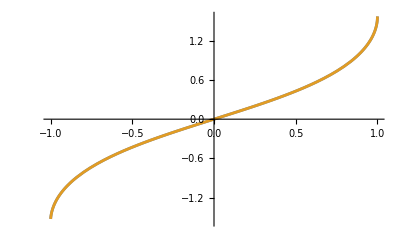

```mathematica
(*Study the poly-log formulas defined after Eq.(3.34) of 2212.13095*)
b2Ref[χ_]=Im[PolyGamma[0, 3+2ⅈ χ/(√(1-χ^2))]];
langevin[x_]=Coth[x]-1/x;
b2[χ_]=Pi/2 langevin[Pi (2χ)/(√(1-χ^2))]-χ √(1-χ^2)(1/2+2/(1+3 χ^2));
Plot[{b2Ref[χ],b2[χ]},{χ,-1,1}]
```

0

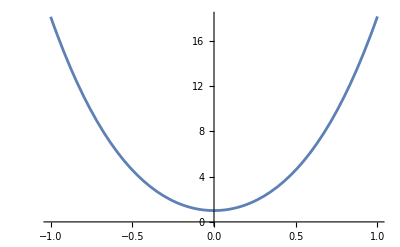

```mathematica
(*value of α01 = f01[χ]/f01[0] from Eq.(3.35) of 2212.13095*)
α01Kerr[χ_]=1/2+(97 χ^2)/18-χ^4/3+π χ (1+3 χ^2) Coth[(2 π χ)/(√(1-χ^2))];
Simplify[1/18(9+9 √(1-χ^2)+97 χ^2+117 √(1-χ^2) χ^2-6 χ^4+54 √(1-χ^2) χ^4+36χ b2[χ]+108 χ^3 b2[χ])-α01Kerr[χ]]
Plot[α01Kerr[χ],{χ,-1,1}]
```